```mathematica
SphericalToCartesian[{r_, θ_, ϕ_}]:={
r * Sin[θ] * Cos[ϕ],
r * Sin[θ] * Sin[ϕ], 
r * Cos[θ]
};
CartesianToSpherical=Function[xyz,
If[xyz[[1]]==0&&xyz[[2]]==0,
{Abs[xyz[[3]]],0,If[xyz[[3]]≥0,0,Pi]},
CoordinateTransform["Cartesian"->"Spherical",xyz]
]
];
(* Create a sphere. Convert it to cartesian coordinates *)
sphereInSphericalCoordinates = Flatten[Table[
{1,x*Pi/180,y*Pi/180},
{y,-90,90,15},
{x,-180,180,15}
], 1];
sphereInCartesianCoordinates = SphericalToCartesian/@sphereInSphericalCoordinates;
(* Rotate the sphere around the cartesian x axis *)
M = RotationTransform[90*Pi/180, {1,0,0}];
sphereInCartesianCoordinates = M/@sphereInCartesianCoordinates;
(* Visualize *)
points = Point/@sphereInCartesianCoordinates;
display = Flatten[{
Sphere[{0, 0, 0}, 0.0],
Blue,Line[{{-1.5,0,0},{1.5,0,0}}],
Green,Line[{{0,-1.5,0},{0,1.5,0}}],
Red,Line[{{0,0,-1.5},{0,0,1.5}}],
Black,points
}, 1];
Graphics3D[display, Axes->True,AxesStyle->{Blue,Green,Red}, RotationAction->"Clip", Boxed->False]
(*
  Convert back to spherical coordinates.
Compute the Cardioid Function.
*)
rotatedSphereInPolarCoordinates = CartesianToSpherical/@sphereInCartesianCoordinates;
rotatedCardioidInPolarCoordinates = ({Cos[#[[2]]/2],#[[2]],#[[3]]})&/@rotatedSphereInPolarCoordinates;
(*
  Convert back to cartesian.
Rotate back to starting position.
*)
rotatedCardioidInCartesianCoordinates = SphericalToCartesian/@rotatedCardioidInPolarCoordinates;
cardioidInCartesianCoordinates = RotationTransform[-90*Pi/180, {1,0,0}]/@rotatedCardioidInCartesianCoordinates;
(*
  Finally, convert back to polar.
Plot ϕ, θ, r as x, y, z
*)
cardioidInPolarCoordinates = CartesianToSpherical/@cardioidInCartesianCoordinates;
ListPointPlot3D[({#[[3]],#[[2]],#[[1]]})&/@cardioidInPolarCoordinates]
```

-Graphics3D-

-Graphics3D-

### Generate Cardioid Table

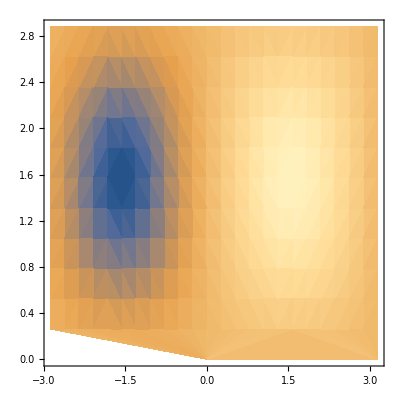

```mathematica
ListDensityPlot[({#[[3]],#[[2]],#[[1]]})&/@cardioidInPolarCoordinates]
```